Last modified on: Wednesday, July 11, 2018 at 3:18

Author Info

Noah Hardwicke

Christopher Wolfram

University of Nottingham

Poster Session Content

FM Demodulation in WL

Transmission of information by radio is commonly implemented with frequency modulation (FM), where the instantaneous frequency of a carrier wave is varied in accordance with a modulating signal. This project aims to implement an FM demodulation function in the Wolfram Language.

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

-Graphics-

Given a modulated wave generated in software, the demodulating function restored the original signal without distortion or artifacts, but results using recorded signals were less faithful due to processing before and after demodulation. Accurately isolating the frequency domain of the carrier wave from a spectrum of frequencies was complicated by noise, and applying filters with set window sizes introduced spurious signals. Improving the former by clipping out background noise could worsen the latter by introducing abrupt boundaries in frequency, which were demodulated into spurious signals.
	Demodulation of raw signal from the SDR produced slightly distorted audio with significant noise, but the audio was discernable and speech could be understood. Noise was reduced by preprocessing the signal with Fourier and inverse Fourier transforms that used an amplitude threshold to clip out background noise. Applying combinations of bandpass and averaging filters to the demodulated signal further helped to reduce noise and clarify the audio, however spurious signals from earlier processing were hardened and amplified. Finally, a filter that clipped data based on the local gradient of the signal was applied to remove, with some success, the spurious signals. The resulting audio was easily intelligible but by no means clean.

Interface the Wolfram Language directly with common software defined radios. Improve filters.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

Theory

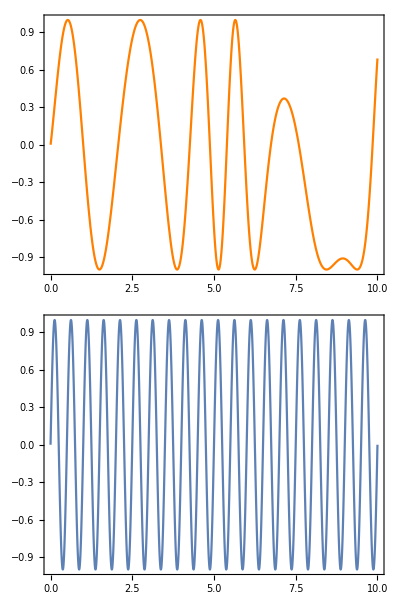
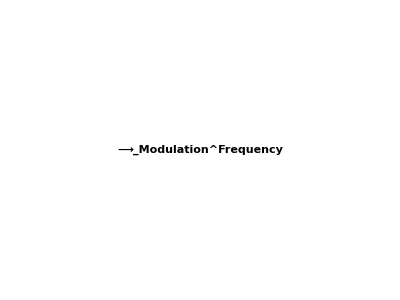
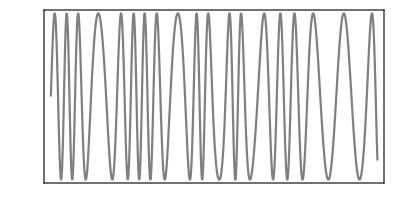

Importing Data

The frequency limitations of sound cards prevent an antenna from being plugged directly into a computer to record MHz frequencies. Instead, an external software defined radio (SDR) unit is used to digitise high-frequency analog signals.

It is unfeasible to process signals of such high bitrates in real time using Mathematica, rather demodulation and filtering is done on recorded data files. Interfacing Mathematica directly with a SDR was achieved, however data could not be read sufficiently quickly to record them, so a third-party application was used to record the data which was then imported into Mathematica. Further work could be done to negate the need for the third-party application.

Processing

Raw modulated signal of 2GHz sample rate was imported.

-Graphics-

Power Spectrum

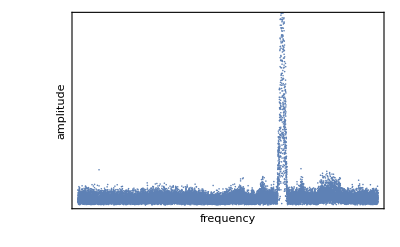

Clipped power spectrum

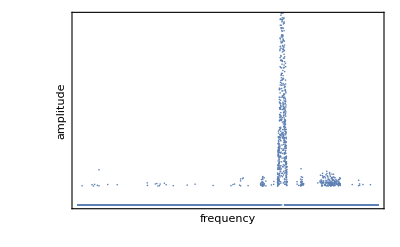

Preprocessed signal

-Graphics-

Demodulated Signal

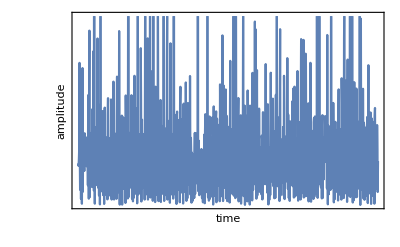

Filtered Signal

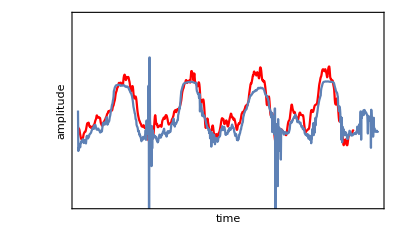

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Main Results in Detail

Given a modulated wave generated in software, the demodulating function restored the original signal without distortion or artifacts, but results using recorded signals were less faithful due to processing before and after demodulation. Accurately isolating the frequency domain of the carrier wave from a spectrum of frequencies was complicated by noise, and applying filters with set window sizes introduced spurious signals. Improving the former by clipping out background noise could worsen the latter by introducing abrupt boundaries in frequency, which were demodulated into spurious signals.
	Demodulation of raw signal from the SDR produced slightly distorted audio with significant noise, but the audio was discernable and speech could be understood. Noise was reduced by preprocessing the signal with Fourier and inverse Fourier transforms that used an amplitude threshold to clip out background noise. Applying combinations of bandpass and averaging filters to the demodulated signal further helped to reduce noise and clarify the audio, however spurious signals from earlier processing were hardened and amplified. Finally, a filter that clipped data based on the local gradient of the signal was applied to remove, with some success, the spurious signals. The resulting audio was easily intelligible but by no means clean.

#### Code

Amplitude pre-filter

```mathematica
signalclipped[list_]:=Module[{ft,threshold},
ft=Fourier[list];
threshold=.1Mean@Abs@ft;
InverseFourier[ft*Boole[Map[#>1.&,Abs[ft]]]]
]
```

FM Demodulator

```mathematica
FMFiltered[list_,samplerate_,{lowfreq_,highfreq_},filterslist_]:=

Module[{A,demod,filtered,filterchain,DCoffsetless},

(* bandpass filter *)
filtered=BandpassFilter[list,20{lowfreq,highfreq},SampleRate->Floor[samplerate/2]];

(* average amplitude of modulated signal *)
A=Abs[filtered]//Mean;

(* demodulation function *)
demod=.5Rescale[Abs[MovingAverage[Differences[filtered],2]/(A √(1.-(filtered⟦2;;-2⟧/A)^2.))],{-1,1}];

(* remove 'DC' offset introduced by demodulation *)
DCoffsetless=demod-Mean[demod];

(* filters *)
filterchain=RightComposition@@(filterslist~Join~{Identity});

(* audio object *)
Audio[filterchain[DCoffsetless],SampleRate->samplerate/2000]

]
```

Remove artifacts introduced by discrete operations (filters and the demodulator itself)

```mathematica
DiscontinuityFilter[list_]:=
Module[{derivative,boolean,mean,sd},
derivative=-Differences[list];
mean=Mean@derivative;
sd=StandardDeviation@derivative;
boolean=Boole[#<mean+sd&/@derivative];
{0}~Join~(boolean⟦2;;⟧*list⟦3;;⟧)+
list⟦;;-2⟧(boolean/.Dispatch[{0->1,1->0}])
]
```

Provide one of:

Link to the GitHub

Explicit code

#### Conclusions in Detail

#### All Visualizations

#### Data Sources Links/References

#### Future Directions

#### Background Info Links/References

#### Keywords

Provide keywords as items

< keyword 1 >

< keyword 2 >

#### Other information